## Useful functions

These functions defines the system that will be studied.

### Definition of the Atom states

There are 3 states : 1 - ground; 2 - excited; 3 - Rydberg.

```mathematica
AtomState={"1","2","3"};
SystemState[n_]:=Flatten[Table[AtomState,{p,1,n}]]
SystemState[2]
```

{1,2,3,1,2,3}

```mathematica
AvailableStates[n_]:=Sort[Permutations[SystemState[n],{n,n}]]
AvailableStates[2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
Anagram[n_]:=Module[{liste=AvailableStates[n]},(* take the list of available states for n atoms *)
Module[{counts=Table[Table[ (* make a table containing ... *)
Count[i,State],{State,AtomState}] (* ... the number of times a "State" appears in ... *)
,{i,liste}]}, (* ... each available configuration *)
Table[ (* make the output table containing ... *)
First[Position[counts,j]][[1]] (* ... the position of the first occurance of an equivalent configuration *)
,{j, counts}]
]
]
```

```mathematica
Anagram[2]
```

{1,2,3,2,5,6,3,6,9}

### Density matrix

Then, one defines the density matrix of N atoms system.

```mathematica
(* The density matrix is hermitian, then it has to obey to the following rules, the diagonal elements are real because of initial conditions *)
SymRules[Num_]:=Drop[DeleteDuplicates[Flatten[ Table[If[m≠n,ρ[n,m][t]->Conjugate[ρ[m,n][t]],0],{m,1,3^Num},{n,m}]]],1]
SymRules[1]
```

{ρ[1,2][t]→Conjugate[ρ[2,1][t]],ρ[1,3][t]→Conjugate[ρ[3,1][t]],ρ[2,3][t]→Conjugate[ρ[3,2][t]]}

```mathematica
SymRules2[Num_]:=Module[{anagram=Anagram[Num]},
Flatten[ Table[ρ[n,m][t]->ρ[anagram[[n]],anagram[[m]]][t],{m,1,3^Num},{n,1,3^Num}]]
]
SymRules2[1]
```

{ρ[1,1][t]→ρ[1,1][t],ρ[2,1][t]→ρ[2,1][t],ρ[3,1][t]→ρ[3,1][t],ρ[1,2][t]→ρ[1,2][t],ρ[2,2][t]→ρ[2,2][t],ρ[3,2][t]→ρ[3,2][t],ρ[1,3][t]→ρ[1,3][t],ρ[2,3][t]→ρ[2,3][t],ρ[3,3][t]→ρ[3,3][t]}

```mathematica
Dens3Level[Num_]:=Array[ρ,{3^Num,3^Num}];
Dens[Num_]:=Block[{DensityMat},
DensityMat=Array[ρ,{3^Num,3^Num}];
Table[DensityMat[[x,y]][t],{x,1,3^Num},{y,1,3^Num}]
]
Dens[1]//MatrixForm
```

(ρ[1,1][t] | ρ[1,2][t] | ρ[1,3][t]
ρ[2,1][t] | ρ[2,2][t] | ρ[2,3][t]
ρ[3,1][t] | ρ[3,2][t] | ρ[3,3][t])

### Rydberg blockade

Here one evaluates the number of atomes in Rydberg states

```mathematica
FindStates[Num_,State_,Val_]:=Block[{p,q},
p=AvailableStates[Num];
q=Length[p];
Flatten[Position[Table[Count[p[[m]],State]==Val,{m,1,q}],True]]]
```

```mathematica
Pr[Num_,Nryd_]:=Sum[ρ[i,i][t],{i,FindStates[Num,"3",Nryd]}];
Pr[2,0]
```

ρ[1,1][t]+ρ[2,2][t]+ρ[4,4][t]+ρ[5,5][t]

```mathematica
Px[Num_,Nryd_,state_]:=Sum[ρ[i,i][t],{i,FindStates[Num,state,Nryd]}];
```

```mathematica
FindStates[2,"2",2][[1]]
```

5

## Liouville - von Neumann equation (Lindbald form)

In this section, we will write the master equation of Molmer's paper (equation (1) of 1302.0682v1 on ariv.org).

### Matrix definition

The main part of this section is here, we compute the σ matrices defined in Molmer’s paper. Then, we easly define the operators using these matices.

```mathematica
(* The famous (σ_(μ⋁))^k matrix of Molmer's paper: transition operator for atom j *)
σμν[Num_,k_,mu_,nu_]:=Table[
If[
i[[k]]==mu  (* initial state *) 
&&
 j[[k]]==nu (* final state *) 
&&
 Drop[i,{k}]==Drop[j,{k}] (* the other atoms does not change *) 
,1,0],{i,AvailableStates[Num]},{j,AvailableStates[Num]}];
```

#### Hamiltonian

```mathematica
H[Num_]:=Sum[Ω1/2*(σμν[Num,i,"1","2"]+σμν[Num,i,"2","1"])+Ω2/2*(σμν[Num,i,"2","3"]+σμν[Num,i,"3","2"]),{i,Num}];
```

#### Detunings

```mathematica
ω0[Num_]:=Table[Sum[If[AvailableStates[Num][[m,r]]=="2",δ1,0]+If[AvailableStates[Num][[m,r]]=="3",δ1+δ2,0],{r,1,Num}],{m,1,3^Num}]
DiagonalMatrix[ω0[2]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | δ1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | δ1+δ2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | δ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 δ1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 δ1+δ2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | δ1+δ2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 δ1+δ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 δ1+2 δ2)

#### Dipole - dipole interaction

```mathematica
Vaa[Num_]:=Δ*Sum[Sum[σμν[Num,k1,"3","3"].σμν[Num,k2,"3","3"],{k1,1,k2-1}],{k2,1,Num}];
Vaa[2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ)

#### Liouvillian

```mathematica
(* We can notice that it requires a density matrix *)
Leg[Dens_, Num_]:=1/2 * Γge * (Sum[2*σμν[Num,i,"1","2"].Dens.σμν[Num,i,"2","1"] - σμν[Num,i,"2","2"].Dens - Dens.σμν[Num,i,"2","2"],{i,1,Num}] )
Lre[Dens_, Num_]:=1/2 * Γre * (Sum[2*σμν[Num,i,"2","3"].Dens.σμν[Num,i,"3","2"] - σμν[Num,i,"3","3"].Dens - Dens.σμν[Num,i,"3","3"],{i,1,Num}] )

Leg[Dens[1],1]//MatrixForm
Tr[Lre[Dens[2],2]]//Simplify (* Must be zero, because by definition, the trace of the density should not change and be unitary *)
```

(Γge ρ[2,2][t] | -1/2 Γge ρ[1,2][t] | 0
-1/2 Γge ρ[2,1][t] | -Γge ρ[2,2][t] | -1/2 Γge ρ[2,3][t]
0 | -1/2 Γge ρ[3,2][t] | 0)

0

### Liouville - von Neumann equation

We are now ready to write the master equation.

```mathematica
(* This function outputs the Optical Bloch equations, one can specify Decay=(True or False) *) 
Equations[Num_,Decay_]:=Block[{Trans,DensityMat,Sym,Liouvillian,ρdot},
Sym=SymRules[Num];
Trans=H[Num]+DiagonalMatrix[ω0[Num]]+Vaa[Num];
DensityMat=Dens[Num];
Liouvillian=Leg[DensityMat,Num]+Lre[DensityMat,Num];

ρdot=(-I*(Trans.DensityMat-DensityMat.Trans)+If[Decay,Liouvillian, DiagonalMatrix[Table[0 ,{m,1,3^Num}]]])/.Sym;

Table[D[ρ[m,n][t],t]==ρdot[[m,n]],{m,1,3^Num},{n,m}](*ρ[m,n]'[t]*)

]
```

```mathematica
(* This code is optimized:
For 3 atomes it takes 1sec, Ilya's program takes 7sec
 For 4 atomes it takes about 1min40, Ilya's program takes 5min *)
Timing[Equations[1,True];][[1]]
```

0.00289

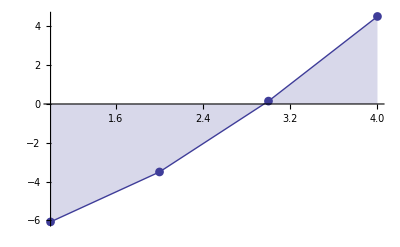
The complexity seems to be exponential
DiscretePlot[Log[Timing[Equations[k,True];][[1]]],{k,1,4},Joined→True,PlotMarkers→Automatic,Axes→{False,True}]
-Graphics-

```mathematica
OpticalBloch1Decay=Equations[1,True];
OpticalBloch2Decay=Equations[2,True];
OpticalBloch3Decay=Equations[3,True];

OpticalBloch1NoDecay=Equations[1,False];
OpticalBloch2NoDecay=Equations[2,False];
OpticalBloch3NoDecay=Equations[3,False];
(*OpticalBloch4NoDecay=Equations[4,True];
OpticalBloch4Decay=Equations[4,False];*)
```

### Intitial conditions

```mathematica
Sigs[Num_]:=Table[Table[KroneckerDelta[m,p]KroneckerDelta[n,q],{p,1,3^Num},{q,1,3^Num}],{m,1,3^Num},{n,m}];
InitialConditions[Num_]:=Table[Dens3Level[Num][[m,n]][0]==If[(m==1 && n== 1),KroneckerDelta[m,n],0],{m,1,3^Num},{n,m}];
InitialExcitedConditions[Num_]:=Module[{AllExcited=FindStates[Num,"2",Num][[1]] },Table[Dens3Level[Num][[m,n]][0]==If[(m==AllExcited&& n== m),KroneckerDelta[m,n],0],{m,1,3^Num},{n,m}]];
Vars[Num_]:=Flatten[Table[Dens3Level[Num][[m,n]][t],{m,1,3^Num},{n,m}]];
InitialConditionsRydStates=Table[Dens3Level[2][[m,n]][0]==If[(m==9 && n== 9),2 KroneckerDelta[m,n],0],{m,1,3^2},{n,m}];
InitialConditionsPStates=Table[Dens3Level[2][[m,n]][0]==If[(m==5 && n== 5),2 KroneckerDelta[m,n],0],{m,1,3^2},{n,m}];
```

## Experiments

Now, we can solve the master equation in several cases (with and without decay, changing the number of atoms)

### Pulses

```mathematica
Ωge[t0_,σt_]:=Ω0*Exp[(-(t-t0/2-σt)^2)/(2 σt^2)]
Ωer[t0_,σt_]:=Ω0*Exp[(-(t-t0/2+σt)^2)/(2 σt^2)]
Chirp[t0_,σt_,ω0_,αt_]:=Ω0*Exp[(-(t-t0/2)^2)/(2 σt^2)]*Cos[ω0*(t-t0/2)+αt*(t-t0/2)^2/2]
Gauss[t0_,σt_]:=Ω0*Exp[(-(t-t0/2)^2)/(2 σt^2)]
SinSq[t0_,σt_]:=Ω0*Piecewise[{{Cos[(π(t-t0))/(2σt)]^2,(t>t0-σt)&&(t<t0+σt)}}]
Step[t0_,σt_]:=Ω0*Piecewise[{{1,(t>t0-σt/2)&&(t<t0+σt/2)}}];
```

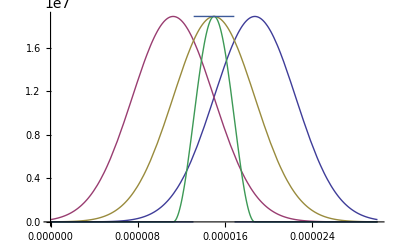

```mathematica
With[{tf=30.*10^(-6)},Plot[Evaluate[Flatten[{Block[{Ω0=2*Pi*3.0*10^6, σt=tf/8,ω0=1,αt=10^12},{Ωge[tf,σt],Ωer[tf,σt],Gauss[tf,σt],SinSq[tf/2,σt],Step[tf/2,σt]}]}]],{t,0,tf}]]
```

### STIRAP Experiments

#### n atoms function

```mathematica
STIRAPn[Numval_,equDecay_,equNoDecay_,δ1val_,δ2val_,Δval_,Ω0val_,tfval_,Γgeval_,Γreval_]:=(

{s1,s2}=With[{ (* s1 is the solution with decayn, and s2 is without decay *)
Num=Numval
},{
With[{
tf=tfval
},
NDSolve[Flatten[{
Block[{
Ω1=Ωge[tf,σt],
Ω2=Ωer[tf,σt],
σt=tf/8,
Ω0=Ω0val,
Γge=Γgeval,
Γre=Γreval,
δ1=δ1val,
δ2=δ2val,
Δ=Δval
},equDecay],InitialConditions[Num]}],Vars[Num],{t,0,tf},MaxSteps->40000]],
With[{
tf=tfval
},NDSolve[Flatten[{
Block[{
Ω1=Ωge[tf,σt],
Ω2=Ωer[tf,σt],
σt=tf/8,
Ω0=Ω0val,
Γge=Γgeval,
Γre=Γreval,
δ1=δ1val,
δ2=δ2val,
Δ=Δval
},equNoDecay],InitialConditions[Num]}],Vars[Num],{t,0,tf}, MaxSteps->40000]]}];
With[{
tf=tfval
},
Grid[{
{
Plot[{
Pr[Numval,0]/.s1 ,(*with decay*) (* this plots the probability of 0 atom in Rydberg state for a Numval number of atoms system *)
Pr[Numval,1]/.s1 (* this plots the probability of 1 atom in Rydberg state for a Numval number of atoms system *)
},{t,0,tf},
ImageSize->Medium,PlotStyle->Thick,
Frame->True,FrameLabel->{{"Populations",None},{"Time (s)",None}},LabelStyle->Bold,
PlotRange->All],
Plot[{
Pr[Numval,0]/.s2,(*without decay*)
Pr[Numval,1]/.s2
},{t,0,tf},
ImageSize->Medium,PlotStyle->Thick,
Frame->True,FrameLabel->{{"Populations",None},{"Time (s)",None}},LabelStyle->Bold,
PlotRange->All]}
,{"Decay","No Decay"}
}]
]
)
```

#### Experiments

```mathematica
Pr[2,0]
Px[2,2,"3"]
```

ρ[1,1][t]+ρ[2,2][t]+ρ[4,4][t]+ρ[5,5][t]

ρ[9,9][t]

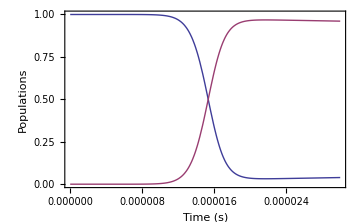
-Graphics- | -Graphics-
Decay | No Decay

```mathematica
(* n atoms experiment *)
(* n=1 *)
With[{
Num=1,(* n=1 *)
equDecay=OpticalBloch1Decay,(* n=1 *)
equNoDecay=OpticalBloch1Decay,(* n=1 *)
δ1=0,
δ2=0,
Δ=1*10^10,
Ω0=2*Pi*3.0*10^6,
tf=30.*10^(-6),
Γge=38.0*10^6,
Γre=1*10^3
},STIRAPn[Num,equDecay,equNoDecay,δ1,δ2,Δ,Ω0,tf,Γge,Γre]]
```

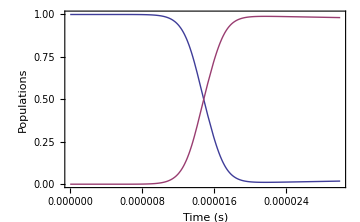
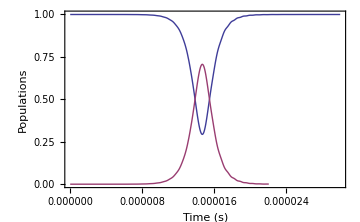
-Graphics- | -Graphics-
Decay | No Decay

```mathematica
(* n=2 *)
With[{
Num=2,(* n=2 *)
equDecay=OpticalBloch2Decay,(* n=2 *)
equNoDecay=OpticalBloch2NoDecay,(* n=2 *)
δ1=0,
δ2=0,
Δ=1*10^10,
Ω0=2*Pi*3.0*10^6,
tf=30.*10^(-6),
Γge=38.0*10^6,
Γre=1*10^3
},STIRAPn[Num,equDecay,equNoDecay,δ1,δ2,Δ,Ω0,tf,Γge,Γre]]
```

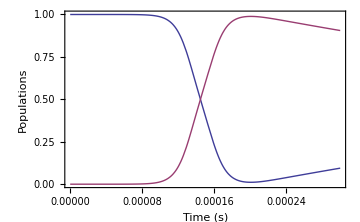
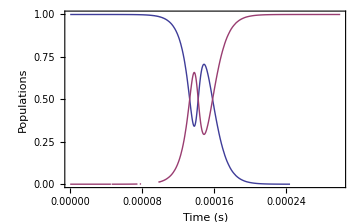
-Graphics- | -Graphics-
Decay | No Decay

```mathematica
(* n=3 *)
With[{
Num=3,(* n=3 *)
equDecay=OpticalBloch3Decay,(* n=3 *)
equNoDecay=OpticalBloch3NoDecay,(* n=3 *)
δ1=0,
δ2=0,
Δ=1*10^10,
Ω0=2*Pi*3.0*10^6,
tf=30.*10^(-5),(*adiabaticity violation*)
Γge=38.0*10^6,
Γre=1*10^3
},STIRAPn[Num,equDecay,equNoDecay,δ1,δ2,Δ,Ω0,tf,Γge,Γre]]
```

```mathematica
(* Press "Alt+," to abort, Mathematica is too long to try to solve the equations for 4 atoms *) 
With[{
Num=4,
equDecay=OpticalBloch4Decay,
equNoDecay=OpticalBloch4NoDecay,
Δ=1*10^10,
Ω0=2*Pi*3.0*10^6,
tf=30.*10^(-6),
Γge=38.0*10^6,
Γre=1*10^3
},STIRAPn[Num,equDecay,equNoDecay,Δ,Ω0,tf,Γge,Γre]]
```

NDSolve::ndsdtc: The time constraint of 1. seconds was exceeded trying to solve for derivatives, so the system will be treated as a system of differential-algebraic equations. You can use Method->{"EquationSimplification"->"Solve"} to have the system solved as ordinary differential equations.

NDSolve::mconly: For the method "IDA", only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

```mathematica
(* Tring to split the solving into time steps, but "MaxSteps->1" seems to be already impossible for 4 atoms *)
s=With[{
split=2,
tf=30.*10^(-6),
Num=1,
Decay=True
},NDSolve[Flatten[{Block[{Ω1=Ωge[tf,σt], Ω2=Ωer[tf,σt],
Ω0=2*Pi*3.0*10^6, 
σt=tf/8,
δ1=0,
δ2=0,
Δ=1*10^10, (* Δ=1*10^6 is a critical value, before, there is no blockade, and after there is *)
Γge=38.0*10^6,
Γre=1*10^3
 },OpticalBloch1NoDecay],InitialConditions[Num]}],Vars[Num],{t,0,tf/split},MaxSteps->Ceiling[40000/split]]];
```

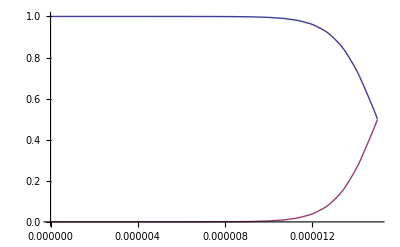

```mathematica
With[{
split=2,
tf=30.*10^(-6),
Num=1
},Plot[{
Pr[Num,0]/.s,
Pr[Num,1]/.s
},{t,0,tf/split}
(*,PlotRange-> {0,1}*)
]]
```

### Chirp Experiments

```mathematica
CHIRPn[Numval_,equDecay_,Δval_,δval_,Ω0val_,αtval_,tfval_,σtval_, Γgeval_,Γreval_]:=(

s=With[{ (* s1 is the solution with decay, and s2 is without decay *)
Num=Numval
},
With[{
tf=tfval
},
NDSolve[Flatten[{
Block[{
Ω1=Gauss[tf,σt]//Simplify,
Ω2=Gauss[tf,σt]//Simplify,
Ω0=Ω0val,
σt=tf/8,
αt=αtval,
Γge=Γgeval,
Γre=Γreval,
Δ=Δval,
δ1=δval+2Pi*αtval*(t-tf/2)^2,
δ2=-δ1
},equDecay],InitialConditions[Num]}],Vars[Num],{t,0,tf},MaxSteps->100000]]];
With[{
tf=tfval,
Num=Numval
},
Plot[{
Px[Num,0,"3"]/.s ,(* this plots the probability of 0 atom in Rydberg state for a Numval number of atoms system *)
Px[Num,1,"3"]/.s, (* this plots the probability of 1 atom in Rydberg state for a Numval number of atoms system *)
Px[Num,2,"3"]/.s
},{t,0,tf},
ImageSize->Medium,
PlotStyle->Thick,
PlotRange->All]
])
```

```mathematica
Px[2,2,"3"]
```

ρ[9,9][t]

```mathematica
(* n=1 *)
With[{
Num=1,(* n=1 *)
equDecay=OpticalBloch1Decay,(* n=1 *)
Δ=0*10^10,
δ=0*10^6,
Ω0=2*Pi*6.0*10^6,
αt=1*10^12,
tf=30.*10^(-6),
Γge=38.0*10^6,
Γre=1*10^3
},CHIRPn[Num,equDecay,Δ,δ,Ω0,αt,tf,Γge,Γre]];
```

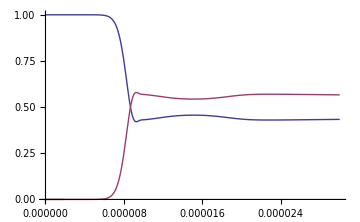

```mathematica
(* n=2 *)
With[{
Num=2,
equDecay=OpticalBloch2Decay,
Δ=1*10^10,
δ=1*10^4,
Ω0=2Pi*6*10^6,
αt=10^12,
tf=30.*10^(-6),
Γge=38.0*10^6,
Γre=1*10^3
},CHIRPn[Num,equDecay,Δ,δ,Ω0,αt,tf,1,Γge,Γre]
]
```

### Rabi oscillations

#### 2 level system

This subsection can reproduce the results of this document: http://www.ph.unimelb.edu.au/~part3/notes/Rabi.pdf using the previously made density matrix formalism. It checks the implementation of the detuning.

```mathematica
DSolve[{
ρ[1,1]'[t]==1/2 ⅈ Ω1 (ρ[1,2][t]-ρ[2,1][t]),
ρ[1,2]'[t]==1/2 ⅈ (Ω1 ρ[1,1][t]-Ω1 ρ[2,2][t]),
ρ[2,1]'[t]==-1/2 ⅈ (Ω1 ρ[1,1][t]-Ω1 ρ[2,2][t]),
ρ[2,2]'[t]==-1/2 ⅈ (Ω1 ρ[1,2][t]-Ω1 ρ[2,1][t]),
ρ[1,1][0]==1,ρ[1,2][0]==0,ρ[2,1][0]==0,ρ[2,2][0]==0
},{ρ[1,1][t],ρ[1,2][t],ρ[2,1][t],ρ[2,2][t]},t]
```

{{ρ[1,1][t]→1/2 (1+Cos[t Ω1]),ρ[1,2][t]→1/2 ⅈ Sin[t Ω1],ρ[2,1][t]→-1/2 ⅈ Sin[t Ω1],ρ[2,2][t]→1/2 (1-Cos[t Ω1])}}

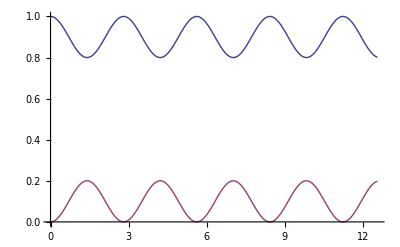

```mathematica
s=With[{
tf=4*Pi,
Num=1,
Decay=True
},NDSolve[Flatten[{Block[{Ω1=1, Ω2=0,
Δ=1*10^10,
δ1=2,δ2=0,
Γge=0,
Γre=0
 },OpticalBloch1Decay],InitialConditions[Num]}],Vars[Num],{t,0,tf}]];
With[{
tf=4*Pi,
Num=1
},Plot[{
ρ[1,1][t]/.s,
ρ[2,2][t]/.s
},{t,0,tf}
(*,PlotRange-> {0,1}*)
]]
```

### Rydberg blocade criterion

Here we are trying to bring out Rydberg blocade using a parameter so called θ=1-p2/(p1+p2)^2, where p1 is the probability to have one excited atom and p2 is the one to have two atoms excited, for a 2 atoms system.
Indeed if the probability to excitate one single atom is given by p, then p2=p^2 and p1=p(1-p) (and p0=(1-p)^2). θ is then equal to zero. But if there is Rydberg blocade, p2 does not remain equal to p^2, that must change the value of θ and would be the desired criterion.

#### Spectra

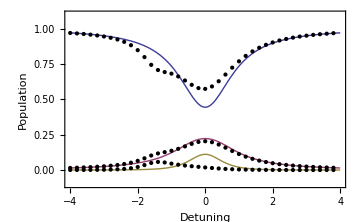

```mathematica
Block[{
n=40,(* number of points in the spectrum *)
scale=5, (* zoom to the center of the spectrum *)
tf=4Pi,(* final time of the experiment, this should be long enough because we are considering stationary solutions *)
Ωval=1,(* Rabi frequency *)
Γreval=1 (* decay value, if it's low, one should increase the final time *)
},
For[i=0,i<n, (* the variable i will be used to sweep the detuning of the laser radiation *)
{s=With[{
Num=2(* number of atoms *)
},NDSolve[Flatten[{Block[{Ω1=0,(* we are only considering the excited and the Rydberg state, there is no interaction with the ground state *)
 Ω2=Ωval,
Δ=3,(* !!! 
dipole-dipole interaction, CHANGE THIS VALUE to {1, 3, 5} to see Rdyberg blocade 
!!! *)
δ1=0,δ2=(i-n/2)/scale,
Γge=0,
Γre=Γreval
 },OpticalBloch2Decay (* for 2 atoms *)
],InitialExcitedConditions[Num] (* we should define new initial conditions, where the only populated state is the one where all the atoms are in the excited state *)
}],Vars[Num],{t,0,tf}]];
{ρ55[i]}=Re[ρ[5,5][t]/.s/.t->tf]; (* 2 atoms in excited state *)
{ρ66[i]}=Re[ρ[6,6][t]/.s/.t->tf];(* 1 atom in excited state and 1 in Rydberg state *)
{ρ99[i]}=Re[ρ[9,9][t]/.s/.t->tf]; (* 2 atoms in Rydberg state *)
};i++];

ρ55Tab=Table[{(i-n/2)/scale,ρ55[i]},{i,0,n-1}];
ρ66Tab=Table[{(i-n/2)/scale,ρ66[i]},{i,0,n-1}];
ρ99Tab=Table[{(i-n/2)/scale,ρ99[i]},{i,0,n-1}];

Plot[{(1-Ωval^2/2/(Ωval^2+2δ^2+Γreval^2/2))^2,(* (1-p)^2 *)
(Ωval^2/2/(Ωval^2+2δ^2+Γreval^2/2))*(1-Ωval^2/2/(Ωval^2+2δ^2+Γreval^2/2)), (* p(1-p) *)
(Ωval^2/2/(Ωval^2+2δ^2+Γreval^2/2))^2 (* p^2 *)
},{δ,-n/(2*scale),n/(2*scale)},Epilog->Map[Point, {ρ55Tab,ρ66Tab,ρ99Tab}],
PlotRange-> {-0.1,1.1},Frame->True,Axes->False,ImageSize->Medium,FrameLabel->{{"Population",None},{"Detuning",None}},LabelStyle->Bold]
]
```

#### Plotting θ with respect to Δ dipole-dipole interaction parameter

```mathematica
Logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)]
Linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)]
```

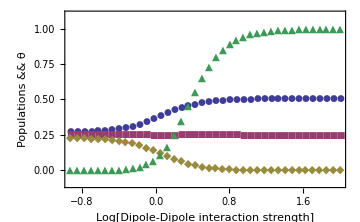

```mathematica
(* Semi-log plot *)
Block[{n=40,init=-1,final=2,scale=5,tf=8Pi,Ωval=1,Γreval=0.25},
ΔTab=Logspace[init,final,n];
For[i=1,i<=n,
{s=With[{
Num=2,
Decay=True
},NDSolve[Flatten[{Block[{Ω1=0, Ω2=Ωval,
Δ=ΔTab[[i]],
δ1=0,δ2=0,
Γge=0,
Γre=Γreval
 },OpticalBloch2Decay],InitialExcitedConditions[Num]}],Vars[Num],{t,0,tf}]];
{ρ55[i]}=Re[ρ[5,5][t]/.s/.t->tf];
{ρ66[i]}=Re[ρ[6,6][t]/.s/.t->tf];
{ρ99[i]}=Re[ρ[9,9][t]/.s/.t->tf];
{θ[i]}=Re[1-(ρ[9,9][t]/(ρ[9,9][t]+ρ[6,6][t])^2)/.s/.t->tf];
};i++];

ρ55Tab=Table[{init+i*(final-init)/n,ρ55[i]},{i,1,n}];
ρ66Tab=Table[{init+i*(final-init)/n,ρ66[i]},{i,1,n}];
ρ99Tab=Table[{init+i*(final-init)/n,ρ99[i]},{i,1,n}];
θTab=Table[{init+i*(final-init)/n,θ[i]},{i,1,n}];

ListPlot[{ρ55Tab,ρ66Tab,ρ99Tab,θTab},PlotRange-> {-0.1,1.1},Joined->False,PlotMarkers->Automatic ,Mesh->All,Frame->True,Axes->False,ImageSize->Medium,FrameLabel->{{"Populations && θ",None},{"Log[Dipole-Dipole interaction strength]",None}},LabelStyle->Bold]
]
```

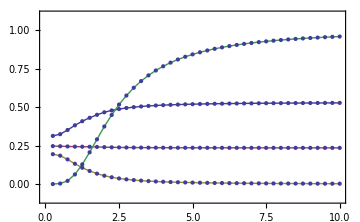

```mathematica
(* Linear plot *)
Block[{n=40,init=0,final=10,scale=5,tf=4Pi,Ωval=1,Γreval=0.5},
ΔTab=Linspace[init,final,n];
For[i=1,i<=n,
{s=With[{
Num=2,
Decay=True
},NDSolve[Flatten[{Block[{Ω1=0, Ω2=Ωval,
Δ=ΔTab[[i]],
δ1=0,δ2=0,
Γge=0,
Γre=Γreval
 },OpticalBloch2Decay],InitialExcitedConditions[Num]}],Vars[Num],{t,0,tf}]];
{ρ55[i]}=Re[ρ[5,5][t]/.s/.t->tf];
{ρ66[i]}=Re[ρ[6,6][t]/.s/.t->tf];
{ρ99[i]}=Re[ρ[9,9][t]/.s/.t->tf];
{θ[i]}=Re[1-(ρ[9,9][t]/(ρ[9,9][t]+ρ[6,6][t])^2)/.s/.t->tf];
};i++];

ρ55Tab=Table[{init+i*(final-init)/n,ρ55[i]},{i,1,n}];
ρ66Tab=Table[{init+i*(final-init)/n,ρ66[i]},{i,1,n}];
ρ99Tab=Table[{init+i*(final-init)/n,ρ99[i]},{i,1,n}];
θTab=Table[{init+i*(final-init)/n,θ[i]},{i,1,n}];

ListPlot[{ρ55Tab,ρ66Tab,ρ99Tab,θTab},PlotRange-> {-0.1,1.1},Joined->True,Mesh->All,Frame->True,Axes->False,ImageSize->Medium]
]
```

### M.Saffman experiment

“For the single atom loading typical parameters currently are : Rb87
5 s–5 p3/2–97 d5/2
sigma + , sigma + coupling to m = 5/2

detuning from 5 p3/2, 1.8 GHz
780 nm Rabi frequency 68 MHz
480 nm Rabi frequency 19 MHz
2 - photon Rabi frequency 0.36 MHz

we load from 3–20 atoms into f = 2 and then pi pulse to | r > followed by pi pulse to f = 1.
Our best results are 65 % single atom in f = 1. Our latest data seem to show we actually have better single atom probability in
f = 1 but we have some loss during blow away of f = 2. We are checking this further.We have also done some adiabatic pulse sequences giving similar results with 65 % success rate.”

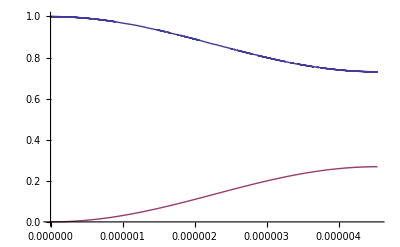

```mathematica
Ω1test=68*10^6; Ω2test=19*10^6;δ1test=1.8*10^9;
ΩR=N[Ω1test*Ω2test/(2*δ1test)];
ΔR=N[(Ω2test^2-Ω1test^2)/(2*2*δ1test)];
T=Pi/Sqrt[ΩR^2+ΔR^2];
s=With[{
tf=T,
Num=1,
Decay=True
},NDSolve[Flatten[{Block[{
Ω1=68*10^6, Ω2=19*10^6,
Δ=0,
δ1=1.8*10^9,δ2=-δ1,
Γge=0*38.0*10^6,
Γre=0*1*10^3
 },OpticalBloch1Decay],InitialConditions[Num]}],Vars[Num],{t,0,tf},MaxSteps->Infinity]];
With[{
tf=T,
Num=1
},Plot[{
ρ[1,1][t]/.s,
ρ[3,3][t]/.s
},{t,0,tf},
PlotRange -> {0,1}
]]
```

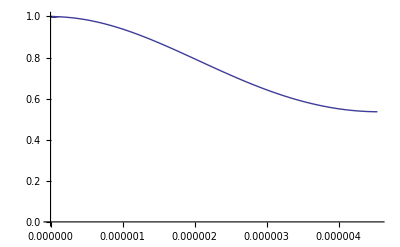

```mathematica
Ω1test=68*10^6; Ω2test=19*10^6;δ1test=1.8*10^9;
ΩR=N[Ω1test*Ω2test/(2*δ1test)];
ΔR=N[(Ω2test^2-Ω1test^2)/(2*2*δ1test)];
T2=Pi/Sqrt[ΩR^2+ΔR^2];
s2=With[{
tf=T2,
Num=2,
Decay=True
},NDSolve[Flatten[{Block[{
Ω1=68*10^6, Ω2=19*10^6,
Δ=0,
δ1=1.8*10^9,δ2=-δ1,
Γge=38.0*10^6,
Γre=1*10^3
 },OpticalBloch2Decay],InitialConditions[Num]}],Vars[Num],{t,0,tf},MaxSteps->Infinity]];
With[{
tf=T2
},Plot[{
ρ[1,1][t]/.s2
},{t,0,tf},
PlotRange -> {0,1}
]]
```

```mathematica
Ω1test=68*10^6; Ω2test=19*10^6;δ1test=1.8*10^9;
ΩR=N[Ω1test*Ω2test/(2*δ1test)];
ΔR=N[(Ω2test^2-Ω1test^2)/(2*2*δ1test)];
T3=Pi/Sqrt[ΩR^2+ΔR^2];
s3=With[{
tf=T3,
Num=3,
Decay=True
},NDSolve[Flatten[{Block[{
Ω1=68*10^6, Ω2=19*10^6,
Δ=0,
δ1=1.8*10^9,δ2=-δ1,
Γge=38.0*10^6,
Γre=1*10^3
 },OpticalBloch3Decay],InitialConditions[Num]}],Vars[Num],{t,0,tf},MaxSteps->Infinity]];
```

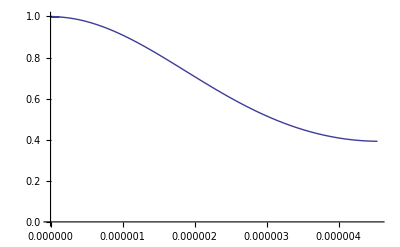

```mathematica
With[{
tf=T3
},Plot[{
ρ[1,1][t]/.s3
},{t,0,tf},
PlotRange -> {0,1}
]]
```

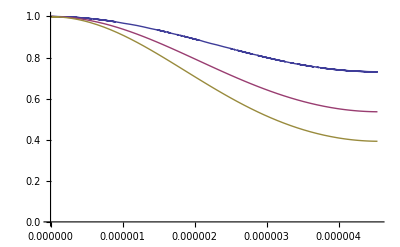

```mathematica
With[{
tf=T3
},Plot[{
ρ[1,1][t]/.s,
ρ[1,1][t]/.s2,
ρ[1,1][t]/.s3
},{t,0,tf},
PlotRange -> {0,1}
]]
```